Last modified on: Wednesday, July 11, 2018 at 2:02

Author Info

Milad Pourrahmani

Carlo Barbieri

University of California, Irvine

Poster Session Content

A New Kind of Chess

The rules of chess have been perfected for more than a millennia to ensure an exciting game every time. These relatively simple rules are capable of producing very interesting and complex dynamics that deserve to be studied in their own rights, not just merely for competition purposes. This project aims at laying down the formalism to capture the game of chess as well as many other board and card games. In accordance with this formalism, a Mathematica chess package has been developed which creates, displays, and evolves a ChessState object using ChessState, ChessPlot, and ChessEvolve functions.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

ChessPlot enables the user to provide options such as board color set, display coordinates, rotate point of view, or extract MatrixForm of a ChessState. In addition,  a list of rule functions is provided which take in a ChessState and output all the possible moves in accordance with the rule they represent.

With this setup, the user is able to setup any ChessEvaluate function and explore the chess space. This open-ended chess design also enables the user to modify the rules with ease so they can explore chess variations such as antichess, atomic chess, and others.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

ChessState

-Graphics-

ChessState[-Graphics-]

ChessPlot

ChessPlot[ChessState[-Graphics-], "WhiteOrientation" → "Left",  "ShowCoordinates" → True, "BoardColorSet" → {LightRed, Pink}, ImageSize → 375]

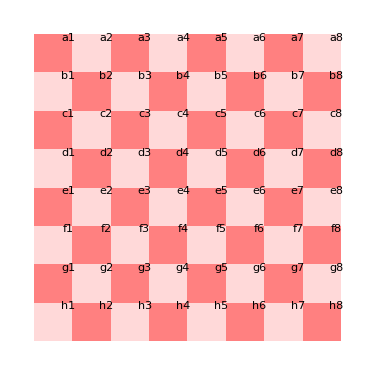

Chess Rules   → Possible Moves Generators
Chess Moves → A Set of Actions

Example:
Any ♘ may move from pos_1 to pos_2 = pos_1 + ∀{{±1, ±2}, {±2, ±1}} if S(pos_2)== ∀{♛, ♜, ♝, ♞, ♟, □}.

possibleMoves = KnightMoves[ChessState[-Graphics-]]
{{b8→□,a6→♞},{b8→□,c6→♞},{g8→□,f6→♞},{g8 → □, h6 → ♞}}

ChessEvolve

ChessEvolve[ChessState[-Graphics-],possibleMoves]

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

You can import chess.m as a package or use Notebook01.nb for code, documentation, and demonstration

https://github.com/Miladiouss/Summer2018Starter/tree/master/ChessPackage

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information